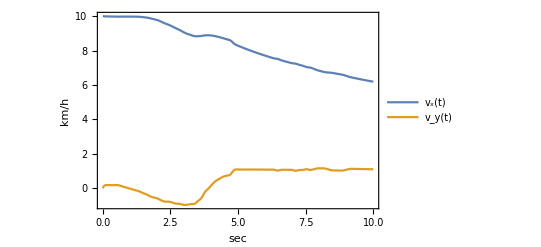

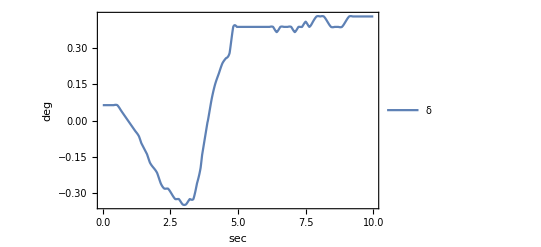

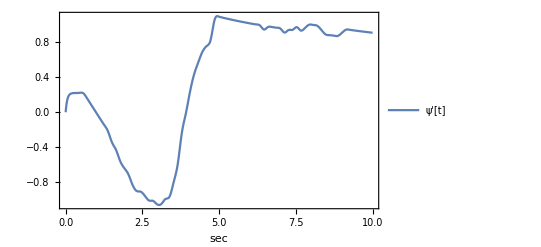

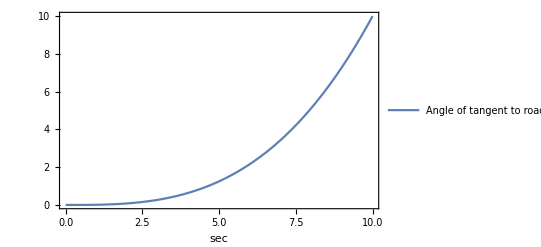

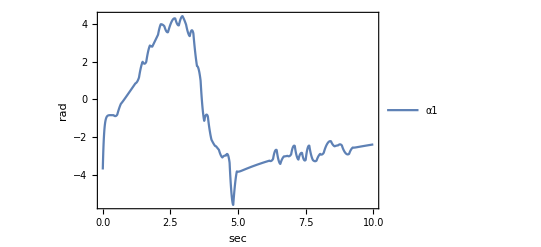

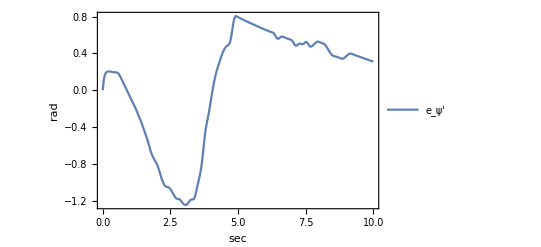

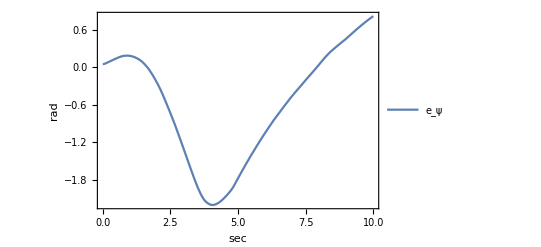

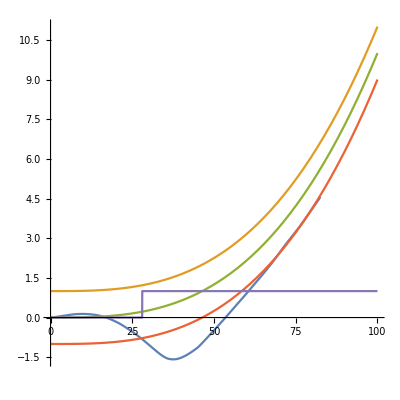

```mathematica
Brake1[t_,τ_,βr_]:=βr/2*(Tanh[20t]-Tanh[20(t-τ)])
(* The following version of Brake[] implements an automatic reaction of the braeaking system if a limit is excieded. The version did not work properly because I may not correctly use the parameters for the break. Adapt it so that it works at the proper time t in the system of equations. *)

Brake[t_,τ0_,τ_,βr_]:=Block[{τ01,τ1,β1},
Piecewise[{{τ01={t};τ1={t+2};β1={1.};Fold[Plus,0,Table[Brake1[t-τ01⟦k⟧,τ1⟦k⟧,β1⟦k⟧],{k,1,Length[τ1]}]],Subscript[e, y][t] > 200},{Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]],Subscript[e, y][t] ≤ 200}}]]

Brake[t_,τ0_,τ_,βr_]:=
Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];

(* there was a problem in your definition of Subscript[β, r]. I replaced it by a unique symbol βr. Mathematica hase sometimes problems with indexed variables like your Subscript[β, r]. Good practice is to avoid all indexed variables in subscript notation. *)

τ0 = {1,10,20,50};
τ = {0.6,3,5,5};
β={0,0,0,.0};
βr= Brake[t,τ0 ,τ ,β];
η = √(1.0-βr^2);

(* the path must be adjusted on your computer *)

q= Import["2.dat"];
q1 = DeleteCases[Table[If[q[[k,1]] == q[[k+1,1]], null ,q[[k+1]]],{k,1,Length[q]-1}],null];
q2 = Map[({First[#]-0.2945,Last[#]})&,q1];
q3 = Interpolation[q2];
δ = 10*(q3[t]);
δ2=Piecewise[{{δ, y[]<αs}, {0, Abs[α]≥αs}}];
rules =
{
Subscript[C, α1]->80000.0,Subscript[C, α2]->80000.0,Subscript[C, α3]->80000.0,Subscript[C, α4]->80000.0,
Subscript[μ, 1]->1.0,Subscript[μ, 2]->1.0,Subscript[μ, 3]->1.0,Subscript[μ, 4]->1.0,
Subscript[F, z1]->26719.0,Subscript[F, z2]->26719.0,Subscript[F, z3]->21295.0,Subscript[F, z4]->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]->5000,Subscript[K, ψ]-> 0,Subscript[ψ, d1] ->-0.12,Subscript[t, lp] -> 1.5
};

(* Slip angle *) 
f1[μ_,F_,C_]:=ArcTan[(3η μ F)/C]/.rules;
Subscript[α, sl1]=f1[Subscript[μ, 1],Subscript[F, z1],Subscript[C, α1]]; Subscript[α, sl2]=f1[Subscript[μ, 2],Subscript[F, z2],Subscript[C, α2]];
Subscript[α, sl3]=f1[Subscript[μ, 3],Subscript[F, z3],Subscript[C, α3]]; Subscript[α, sl4]=f1[Subscript[μ, 4],Subscript[F, z4],Subscript[C, α4]];

f2[δ_,l_]:=(y'[t] + l ψ'[t])/x'[t]-δ/.rules;
α1=f2[δ,Subscript[l, f]]; Subscript[α, 2]=f2[δ,Subscript[l, f]];
Subscript[α, 3]=f2[0,-Subscript[l, r]]; Subscript[α, 4]=f2[0,-Subscript[l, r]];

(* Tire  Lateral Force *)
f3[C_,α_,μ_,F_,αs_]:=Piecewise[{{- C Tan[α]+ C^2/(3η μ F) Abs[Tan[α]] Tan[α]- C^3/(27(η μ F)^2)Tan[α]^3, Abs[α]<αs}, {-η μ F Sign[α], Abs[α]≥αs}}];
Subscript[f, y1]=f3[Subscript[C, α1],α1,Subscript[μ, 1],Subscript[F, z1],Subscript[α, sl1]]/.rules; Subscript[f, y2]=f3[Subscript[C, α2],Subscript[α, 2],Subscript[μ, 2],Subscript[F, z2],Subscript[α, sl2]]/.rules;
Subscript[f, y3]=f3[Subscript[C, α3],Subscript[α, 3],Subscript[μ, 3],Subscript[F, z3],Subscript[α, sl3]]/.rules; Subscript[f, y4]=f3[Subscript[C, α4],Subscript[α, 4],Subscript[μ, 4],Subscript[F, z4],Subscript[α, sl4]]/.rules;

(* Tire  Longitudinal Force *) 
f4[μ_,F_]:=βr μ F/.rules;
Subscript[f, x1]=f4[Subscript[μ, 1],Subscript[F, z1]]/.rules; Subscript[f, x2]=f4[Subscript[μ, 2],Subscript[F, z2]]/.rules;
Subscript[f, x3]=f4[Subscript[μ, 3],Subscript[F, z3]]/.rules; Subscript[f, x4]=f4[Subscript[μ, 4],Subscript[F, z4]]/.rules;

(* Long. and Lat. Tot. Forces *)
Subscript[F, x1] =Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ]; Subscript[F, x2] =Subscript[f, x2] Cos[δ] - Subscript[f, y2] Sin[δ];
Subscript[F, x3] =Subscript[f, x3] Cos[0] - Subscript[f, y3] Sin[0]; Subscript[F, x4] =Subscript[f, x4] Cos[0] - Subscript[f, y4] Sin[0];

Subscript[F, y1] =Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ]; Subscript[F, y2] =Subscript[f, x2] Sin[δ] + Subscript[f, y2] Cos[δ];
Subscript[F, y3] =Subscript[f, x3] Sin[0] + Subscript[f, y3] Cos[0]; Subscript[F, y4] =Subscript[f, x4] Sin[0] + Subscript[f, y4] Cos[0];

(*phi = (0) + (Subscript[Ce, 0]*x[t]) +(1/2 Subscript[Ce, 1]*(x[t])^2)
u = (0) + phi*x[t] + (1/2 Subscript[Ce, 0]*(x[t])^2) + (1/6 Subscript[Ce, 1]*(x[t])^3);*)
u[t_] :=  0.01 t^3;
(* Equations of Motion *)
Eq1 = m x''[t]== m y'[t]ψ'[t] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4];
Eq2 = m y''[t] == -m x'[t] ψ'[t] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4];
Eq3 =Subscript[J, z] ψ''[t] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r](Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)( Subscript[F, x2] -Subscript[F, x1] - Subscript[F, x3] + Subscript[F, x4]);
Eq4 = Subscript[e, ψ]'[t]==( ψ'[t]-u''[t]);
Eq5 = Subscript[e, y]'[t]==(*ψ'[t]-0.0002 t*)y'[t] Cos[Subscript[e, ψ][t]] + x'[t]Sin[Subscript[e, ψ][t]];

motionEq ={Eq1,Eq2,Eq3,Eq4,Eq5}/.rules;
time =69.9;
initCond={x[0]==0.1,x'[0]==10,y[0]==0.0,y'[0]==0.00,ψ[0]==0.00,ψ'[0]==0, Subscript[e, ψ][0] == 00.05, Subscript[e, y][0] == -1};
solution=NDSolve[Flatten[{motionEq/.rules,initCond}],{x,y,ψ,Subscript[e, ψ],Subscript[e, y]},{t,0,time}];

FlagY =Piecewise[{{0, u[t]+ 1>y[t] > u[t]-1}, {1, True}}];
Subscript[Flag, ey] =Piecewise[{{1, Subscript[e, y][t] > 200}, {0, Subscript[e, y][t]≤  200}}];
Subscript[Flag, slip1] =Piecewise[{{0, 0.07>α1 > -0.07}, {1, True}}];
Subscript[Flag, slip2] =Piecewise[{{0, 0.07>Subscript[α, 2] > -0.07}, {1, True}}];
Subscript[Flag, slip3] =Piecewise[{{0, 0.07>Subscript[α, 3] > -0.07}, {1, True}}];
Subscript[Flag, slip4]=Piecewise[{{0, 0.07>Subscript[α, 4] > -0.07}, {1, True}}];

f5[x_,y_,l2_,s1_,s2_]:=Plot[Evaluate[{x,y}/.solution],{t,0,10},Frame->True,FrameLabel->{sec,l2},PlotLegends->{s1,s2},PlotRange->All] ;
f5[x[t],y[t],m,x[t],"y(t)"];
f5[x'[t],y'[t],"km/h","v_x(t)","v_y(t)"]
f5[x''[t],y''[t],"m/s^2","a_x(t)","a_y(t)"];
f5[δ,,"deg","δ",""]
f5[ψ'[t],,"","ψ'[t]",""]
f5[u[t],,"","Angle of tangent to road centerline",""]
Plot1 = ParametricPlot[{{x[t],y[t]}/.solution},{t,0,time},PlotRange-> All,AspectRatio->Full];
Plot2 = ParametricPlot[{{u[t]}},{t,0,time},PlotRange-> All];
Show[{Plot1,Plot2}, PlotRange-> All];
f5[α1*180/π,,"rad","α1",""]
f5[Subscript[e, ψ]'[t]/.solution,,"rad","e_ψ'",""]
f5[Subscript[e, ψ][t]/.solution,,"rad","e_ψ",""]

f5[Subscript[Flag, ey],,"-","Flag_ey",""];
f5[u[t],,"","psid",""];
Plot[Evaluate[{Subscript[Flag, slip1],Subscript[Flag, slip2],Subscript[Flag, slip3],Subscript[Flag, slip4]}/.solution],{t,0,time},Frame->True,FrameLabel->{sec,""},PlotLegends->{"Flag_slip1","Flag_slip2","Flag_slip3","Flag_slip4"},PlotRange->All] ;

(* The upper parabola is the left boundary of the road. The mid parabola is the center of the road. The bottom parabola is the lower bound of the road. There isa flag FlagY tetecting the crossing of the mid of the road. Your flag Subscript[Flag, ey] detects a value of ey[t]. The road is represented using time as parameter. This needs the knowledge of the maximal value of the elongation x as a function of t (here about 700). To match the scales there must be a reduction of x by a factor 10 or an amplification of the x-coordinate of the road by 10 which is used here. The y coordinate of the road uses a scaled version of your curve using C1 and C0 *)

P1 = ParametricPlot[{{x[t],y[t]}/.solution,{10t,u[t]+1},{10t,u[t]},{10t, u[t]-1},{10 t,FlagY/.solution}(*{10t, Subscript[e, y][t]/.solution}{t,Sqrt[(x[t])^2+(y[t])^2]/.solution}*)},{t,0,10},AspectRatio->1,PlotRange->All]
f5[Subscript[e, y][t]/.solution,,"m","e_y",""]
f5[ψ[t]+0.0001 t^2/.solution,,"m","e_y",""]
```

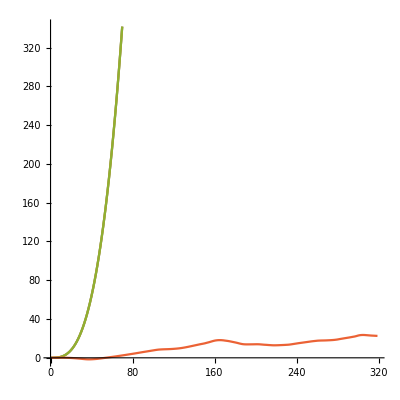

```mathematica
P1 = ParametricPlot[{{t,u[t]},{t,u[t]},{t, u[t]},{x[t],y[t]}/.solution(*{10t, Subscript[e, y][t]/.solution}{t,Sqrt[(x[t])^2+(y[t])^2]/.solution}*)},{t,0,time},AspectRatio->1,PlotRange->All]
```

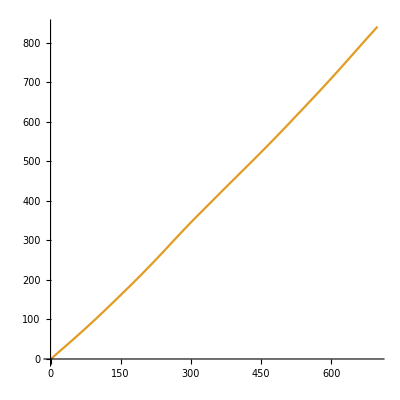

```mathematica
P1 = ParametricPlot[{{10t, x[t]+Subscript[e, y][t]/.solution}},{t,0,time},AspectRatio->1,PlotRange->All]
```